# γγ Scattering

## Notation, η, etc.

```mathematica
(* Define notation to be used throughout this notebook*)
<<Notation`
Notation[Subscript[g_, x_,y_] ⟺ g_[[x_,y_]]]
Notation[g_^(x_,y_) ⟺ Inverse[g_][[x_,y_]]]
Notation[Subscript[x_, μ_] ⟺ Lower[x_][[μ_]]]
Notation[Subscript[F_, a_,b_](k_,n_,λ_,m_) ⟺ F_[k_,n_,λ_,m_][[a_,b_]]];
h[a_,b_]:=h[b,a]/;Not[OrderedQ[{a,b}]];
h[a_,b_]:=0/;Or[a==1,b==1];
```

```mathematica
g=1/z^2{{1,0,0,0,0},{0,0,-1/2,0,0},{0,-1/2,0,0,0},{0,0,0,1,0},{0,0,0,0,1}};
η={{0,-1/2,0,0},{-1/2,0,0,0},{0,0,1,0},{0,0,0,1}};
X={pl,mn,pp1,pp2};
sProd[x_,y_]:=sProd[x,y]=Simplify[∑_(μ=1)^4 ∑_(ν=1)^4 x[[μ]] y[[ν]] Subscript[η, μ,ν]];
Lower[y_]:=Lower[y]=Table[∑_(j=1)^4 Subscript[η, i,j] y⟦j⟧,{i,1,4}];
```

## Kinematics

```mathematica
(* Kinematics of the incoming photons*)
```

```mathematica
k1={√s,-Q1^2/(√s),0,0};k2={-Q2^2/(√s),√s,0,0};
n1={{0,0,1,0},{0,0,0,1},1/Q1{√s,Q1^2/(√s),0,0}};
n2={{0,0,1,0},{0,0,0,1},1/Q2{Q2^2/(√s),√s,0,0}};
```

```mathematica
(* Kinematics of the outgoing photons*)
k3γ=-{√s,(qx^2+qy^2-Q3^2)/(√s),qx,qy};k4γ=-{(qx^2+qy^2-Q4^2)/(√s),√s,-qx,-qy};
n3γ={{0,2 qx/(√s),1,0},{0,2 qy/(√s),0,1},1/Q3{√s,(Q3^2+qx^2+qy^2)/(√s),qx,qy}};
n4γ={{-2 qx/(√s),0,1,0},{-2 qy/(√s),0,0,1},1/Q4{(Q4^2+qx^2+qy^2)/(√s),√s,-qx,-qy}};
```

```mathematica
(* Kinematics of the outgoing meson *)
k3Meson=-{√s,(qx^2+qy^2+m3^2)/(√s),qx,qy};k4Meson=-{(qx^2+qy^2+m4^2)/(√s),√s,-qx,-qy};
n3Meson={{0,2 qx/(√s),1,0},{0,2 qy/(√s),0,1},1/m3{√s,(-m3^2+qx^2+qy^2)/(√s),qx,qy}};
n4Meson={{-2 qx/(√s),0,1,0},{-2 qy/(√s),0,0,1},1/m4{(-m4^2+qx^2+qy^2)/(√s),√s,-qx,-qy}};
```

## AdS States

Defining AdS

```mathematica
Unprotect@Print;
Print = Null;
<<xAct`xPert`;
<<xAct`xPand`;
<<xAct`SplitExpression`.1d ;
(* Define a 5d manifold M *)
DefManifold[M,5,{a,b,c,d,m,n}];
(* We also define a metric on this manifold,with negative determinant and associated covariant derivative CD.This derivative is extended to act on tensor densities defined using the determinant of the metric g in the basis AIndex: *)
DefMetric[-1,g[-m,-n],CD,{";","∇"},WeightedWithBasis->AIndex];
DefParameter[z];
(* Use the same notation as Alfonso *)
$CovDFormat="Prefix";
(* Because we shall work with a single covariant derivative operator,we can choose a simpler output for the geometric tensors *)
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
(* Definition of the warp factor A. Later we set it as -Log[z]*)
DefTensor[A[],M,PrintAs->"A"];
(* Define the U(1) gauge field *)
DefTensor[V[-a],M,PrintAs->"V"];
DefTensor[Vz[],M,PrintAs->"V_z"];
(* colour in blue the perturbative orders *)
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
(* splitting code *)
DefManifold[flat,4,{μ,ν,λ,ρ,σ,α,β}];
DefMetric[-1,η[-μ,-ν],CDflat,{"|","𝒟"}];
DefTensor[Vflat[-μ],flat,PrintAs->"V"];
η/:PD[_][η[__]]:=0;
A/:PD[_][A[]]:=0;
DefSplitting[AAdS,M->{z,flat}];
SplittingRules[AAdS,
{g[-z,-z]->Exp[2A[]],
g[-z,-μ]->0,
g[-μ,-z]->0,
g[-μ,-ν]->Exp[2A[]]η[-μ,-ν],
g[z,z]->Exp[-2A[]],
g[z,μ]->0,
g[μ,z]->0,
g[μ,ν]->Exp[-2A[]]η[μ,ν],
V[-z]->Vz[],
V[-μ]->Vflat[-μ]
}
];
AddTensorDependencies[{g,A,V,Vz,Vflat},{z}];
(* Define metric perturbation *)
DefMetricPerturbation[g,δg,ϵ];
DefTensorPerturbation[δV[LI[order],-a],V[-a],M];
time=ComputeCurvatureTensors[AAdS]//Timing//First;
Unprotect[Print];
Print=.;
Protect[Print];
Print["Splitting curvature tensors computed in ", time, " seconds"]
```

Splitting curvature tensors computed in 1.1455 seconds

Computing Normalizable modes

```mathematica
(* Definition of Subscript[F, ab]*)
F[a_?AIndexQ,b_?AIndexQ]:=CD[a][V[b]]-CD[b][V[a]];
```

```mathematica
(*U(1) gauge field lagrangian*)
ℒ=-1/4 √(-Detg[])F[-a,-b]F[a,b];
```

```mathematica
(* Use variational method to get the EOMs *)
ExpandPerturbation@Perturbation@ℒ/.δg[__]->0;
1/(√(-Detg[]))VarD[δV[LI[1],m],CD][%]/.delta[Times[-1,LI[1]],LI[1]]->1//ContractMetric//Simplification;
eom=%
```

∇_a ∇^a V |  
m-∇_a ∇_m V | a

```mathematica
(*Compute the EOM componentwise*)
SplitExpression[AAdS,Fun->SeparateMetric[],ComponentsListQ->True][eom];
splittedEOM=%
```

-∇_n$4955 ∇_z V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
z→-ⅇ^(-2 A) ∂_z ∂_α V | α
 +ⅇ^(-2 A) ∂_α ∂^α V_z
-∇_n$4955 ∇_μ V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
μ→ⅇ^(-2 A) ∂_z A ∂_z V |  
μ-ⅇ^(-2 A) ∂_z ∂_μ V_z+ⅇ^(-2 A) ∂_z ∂_z V |  
μ+ⅇ^(-2 A) ∂_α ∂^α V |  
μ-ⅇ^(-2 A) ∂_α ∂_μ V | α
 -ⅇ^(-2 A) ∂_z A ∂_μ V_z

```mathematica
(*Apply the gauge conditions*)
splittedEOM/.{Vz[]->0,ParamD[z][PD[-α][Vflat[α]]]->0,PD[-α][PD[-μ][Vflat[α]]]->0}
```

-∇_n$4955 ∇_z V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
z→0
-∇_n$4955 ∇_μ V | n$4955
 +∇_n$4955 ∇^n$4955 V |  
μ→ⅇ^(-2 A) ∂_z A ∂_z V |  
μ+ⅇ^(-2 A) ∂_z ∂_z V |  
μ+ⅇ^(-2 A) ∂_α ∂^α V |  
μ

```mathematica
(*Subscript[V, μ]=Subscript[n, μ] f[z] ⅇ^(ⅈp.x)*)
```

```mathematica
(*Find normalizable mode of U(1) gauge field *)
ClearAll[m];
fSol=DSolve[{m^2 f[x]-1/x f'[x]+f''[x]==0,f[0]==0},f,x][[1]]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{f→Function[{x},x BesselJ[1,m x] C[1]]}

```mathematica
(* We have a wall at z = zf to mimic confinement effects. If we impose the derivative to be zero at this wall we can establish a relationship between the mass of meson and the position of this wall.*)
(f'[zf]/.fSol//FullSimplify)
```

m zf BesselJ[0,m zf] C[1]

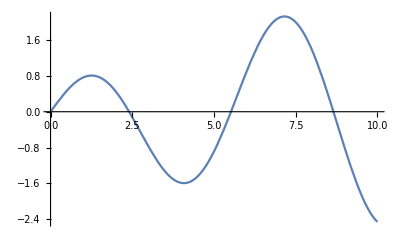

```mathematica
(* Plot the previous function to find zeros *)
Plot[x BesselJ[0,x],{x,0,10}]
```

```mathematica
FindRoot[x BesselJ[0,x],{x,2}]
```

{x→2.40483}

```mathematica
(* Given the mass m of the meson, zf = ζ / m*)
(*ζ = 2.404825557695773;*)
```

```mathematica
(*We now find C[1] through normalization of the integral 14 in the notes provided my Miguel *)
```

```mathematica
Integrate[1/z(f[z]/.fSol)^2,{z,0,zf}]//FullSimplify
(*m zf = ζ which is a root of x BesselJ[0,x]*)
%/.zf->ζ/m//Expand
%/.{ζ^2 BesselJ[0,ζ]^2->0,ζ BesselJ[0,ζ]->0}
Solve[%==1,C[1]][[2]]
```

(zf (m zf BesselJ[0,m zf]^2-2 BesselJ[0,m zf] BesselJ[1,m zf]+m zf BesselJ[1,m zf]^2) C[1]^2)/(2 m)

(ζ^2 BesselJ[0,ζ]^2 C[1]^2)/(2 m^2)-(ζ BesselJ[0,ζ] BesselJ[1,ζ] C[1]^2)/m^2+(ζ^2 BesselJ[1,ζ]^2 C[1]^2)/(2 m^2)

(ζ^2 BesselJ[1,ζ]^2 C[1]^2)/(2 m^2)

{C[1]→(√2 m)/(ζ BesselJ[1,ζ])}

```mathematica
fNAdS[z_,m_]:=(√2 m)/(ζ BesselJ[1,ζ])z BesselJ[1,m z];
dfNAdS[z_,m_]:=(√2 m^2)/(ζ BesselJ[1,ζ])z BesselJ[0,m z];
```

```mathematica
FNAdS[k_,n_,λ_,m_]:=FNAdS[k,n,λ,m]=Exp[ⅈ sProd[k,X]]{ dfNAdS[z,m]{0,Subscript[n[[λ]], 1],Subscript[n[[λ]], 2],Subscript[n[[λ]], 3],Subscript[n[[λ]], 4]},{- dfNAdS[z,m] Subscript[n[[λ]], 1],0,ⅈ fNAdS[z,m](Subscript[k, 1] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 1]),ⅈ fNAdS[z,m](Subscript[k, 1] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 1]),ⅈ fNAdS[z,m](Subscript[k, 1] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 1])},{-dfNAdS[z,m] Subscript[n[[λ]], 2],ⅈ fNAdS[z,m](Subscript[k, 2] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 2]),0,ⅈ fNAdS[z,m](Subscript[k, 2] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 2]),ⅈ fNAdS[z,m](Subscript[k, 2] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 2])},{- dfNAdS[z,m] Subscript[n[[λ]], 3],ⅈ fNAdS[z,m](Subscript[k, 3] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 3]),ⅈ fNAdS[z,m](Subscript[k, 3] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 3]),0,ⅈ fNAdS[z,m](Subscript[k, 3] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 3])},{- dfNAdS[z,m] Subscript[n[[λ]], 4],ⅈ fNAdS[z,m](Subscript[k, 4] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 4]),ⅈ fNAdS[z,m](Subscript[k, 4] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 4]),ⅈ fNAdS[z,m](Subscript[k, 4] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 4]),0}}
```

Nonnormalizable modes

```mathematica
fNNAdS[z_,Q_]:=Q z BesselK[1,Q z];
dfNNAdS[z_,Q_]:=-Q^2 z BesselK[0,Q z];
```

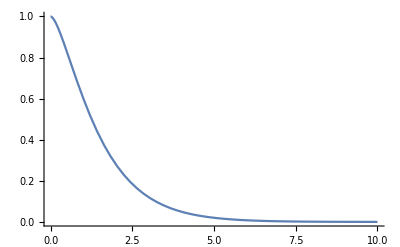

```mathematica
(* Ok this is the analogous of what I find in IHQCD *)
Plot[x BesselK[1,x],{x,0,10},PlotRange->All]
```

```mathematica
FNNAdS[k_,n_,λ_,Q_]:=FNNAdS[k,n,λ,Q]=Exp[ⅈ sProd[k,X]]{ dfNNAdS[z,Q]{0,Subscript[n[[λ]], 1],Subscript[n[[λ]], 2],Subscript[n[[λ]], 3],Subscript[n[[λ]], 4]},{- dfNNAdS[z,Q] Subscript[n[[λ]], 1],0,ⅈ fNNAdS[z,Q](Subscript[k, 1] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 1]),ⅈ fNNAdS[z,Q](Subscript[k, 1] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 1]),ⅈ fNNAdS[z,Q](Subscript[k, 1] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 1])},{-dfNNAdS[z,Q] Subscript[n[[λ]], 2],ⅈ fNNAdS[z,Q](Subscript[k, 2] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 2]),0,ⅈ fNNAdS[z,Q](Subscript[k, 2] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 2]),ⅈ fNNAdS[z,Q](Subscript[k, 2] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 2])},{- dfNNAdS[z,Q] Subscript[n[[λ]], 3],ⅈ fNNAdS[z,Q](Subscript[k, 3] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 3]),ⅈ fNNAdS[z,Q](Subscript[k, 3] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 3]),0,ⅈ fNNAdS[z,Q](Subscript[k, 3] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 3])},{- dfNNAdS[z,Q] Subscript[n[[λ]], 4],ⅈ fNNAdS[z,Q](Subscript[k, 4] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 4]),ⅈ fNNAdS[z,Q](Subscript[k, 4] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 4]),ⅈ fNNAdS[z,Q](Subscript[k, 4] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 4]),0}}
```

Computing F_ab g^bc F_cd h^ad

```mathematica
(* Double vector Meson production Upper part of the diagram*)
Print["DVMP - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,1,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,2,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNAdS, c,d](k3Meson,n3Meson,3,m3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
```

DVMP - upper part of the Witten diagram

-(ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (m3^2+Q1^2+qx^2+qy^2))/(2 √s)) m3 Q1 z^4 BesselJ[1,m3 z] BesselK[1,Q1 z] h[3,3])/(2 √2 ζ BesselJ[1,ζ])

0

0

0

-(ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (m3^2+Q1^2+qx^2+qy^2))/(2 √s)) m3 Q1 z^4 BesselJ[1,m3 z] BesselK[1,Q1 z] h[3,3])/(2 √2 ζ BesselJ[1,ζ])

0

0

0

(ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (m3^2+Q1^2+qx^2+qy^2))/(2 √s)) m3 Q1 z^4 BesselJ[0,m3 z] BesselK[0,Q1 z] h[3,3])/(2 √2 ζ BesselJ[1,ζ])

```mathematica
(* Double vector Meson production lower part of the diagram*)
Print["DVMP - lower part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1,m4)h[a,d]//Collect[#,s,FullSimplify]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,1,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,2,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNAdS, c,d](k4Meson,n4Meson,3,m4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
```

DVMP - lower part of the Witten diagram

-(ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (m4^2+Q2^2+qx^2+qy^2))/(2 √s)) m4 Q2 z^4 BesselJ[1,m4 z] BesselK[1,Q2 z] h[2,2])/(2 √2 ζ BesselJ[1,ζ])

0

0

0

-(ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (m4^2+Q2^2+qx^2+qy^2))/(2 √s)) m4 Q2 z^4 BesselJ[1,m4 z] BesselK[1,Q2 z] h[2,2])/(2 √2 ζ BesselJ[1,ζ])

0

0

0

(ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (m4^2+Q2^2+qx^2+qy^2))/(2 √s)) m4 Q2 z^4 BesselJ[0,m4 z] BesselK[0,Q2 z] h[2,2])/(2 √2 ζ BesselJ[1,ζ])

```mathematica
(* Photon scattering Upper part of the diagram*)
Print["Photon scattering - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,1,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,2,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k1,n1,3,Q1)g^(b,c)Subscript[FNNAdS, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
```

Photon scattering - upper part of the Witten diagram

-1/4 ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)) Q1 Q3 z^4 BesselK[1,Q1 z] BesselK[1,Q3 z] h[3,3]

0

0

0

-1/4 ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)) Q1 Q3 z^4 BesselK[1,Q1 z] BesselK[1,Q3 z] h[3,3]

0

0

0

-1/4 ⅇ^(-ⅈ pp1 qx-ⅈ pp2 qy+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)) Q1 Q3 z^4 BesselK[0,Q1 z] BesselK[0,Q3 z] h[3,3]

```mathematica
(* Photon scattering lower part of the diagram*)
Print["Photon scattering - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,1,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,2,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[FNNAdS, a,b](k2,n2,3,Q2)g^(b,c)Subscript[FNNAdS, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&//Coefficient[#,s]&
```

Photon scattering - upper part of the Witten diagram

-1/4 ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (Q2^2-Q4^2+qx^2+qy^2))/(2 √s)) Q2 Q4 z^4 BesselK[1,Q2 z] BesselK[1,Q4 z] h[2,2]

0

0

0

-1/4 ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (Q2^2-Q4^2+qx^2+qy^2))/(2 √s)) Q2 Q4 z^4 BesselK[1,Q2 z] BesselK[1,Q4 z] h[2,2]

0

0

0

-1/4 ⅇ^(ⅈ pp1 qx+ⅈ pp2 qy+(ⅈ mn (Q2^2-Q4^2+qx^2+qy^2))/(2 √s)) Q2 Q4 z^4 BesselK[0,Q2 z] BesselK[0,Q4 z] h[2,2]

## AdS Black Disk

```mathematica
(*Solve L in terms of z, zbar and l*)
```

```mathematica
Solve[Cosh[L]==(z^2+zbar^2)/(2z zbar),L]
```

{{L→ConditionalExpression[-ArcCosh[(z^2+zbar^2)/(2 z zbar)]+2 ⅈ π C[1],C[1]∈ℤ]},{L→ConditionalExpression[ArcCosh[(z^2+zbar^2)/(2 z zbar)]+2 ⅈ π C[1],C[1]∈ℤ]}}

```mathematica
(*Rescale z and zbar before plotting*)
z^((1-ω)/(1+ω))s^(-ω/(1+ω))/.z->λ/(√s)//FullSimplify[#,Assumptions->{ω>0,λ>0,s>0}]&
z^((1+ω)/(1-ω))s^(ω/(1-ω))/.z->λ/(√s)//FullSimplify[#,Assumptions->{ω>0,λ>0,s>0}]&
```

λ^(-1+2/(1+ω))/(√s)

s^(ω/(1-ω)) (λ/(√s))^((1+ω)/(1-ω))

```mathematica
(*plot of the region of allowed z and zbar*)
Manipulate[Plot[{λ^((1-ω)/(1+ω)),λ^((1+ω)/(1-ω))},{λ,0,3},PlotLegends->{"λ^((1 - ω)/(1 + ω))","λ^((1 + ω)/(1 - ω))"}],{ω,0.1,2}]
```

```mathematica
BesselJ[0,0]
```

1

```mathematica
Integrate[Sinh[L],{L,Abs[Log[z/zbar]],ω Log[z zbar s]}]//FullSimplify[#,Assumptions->{ω>0,s>0,z>0,zbar>0}]&
```

-Cosh[Abs[Log[z/zbar]]]+Cosh[ω Log[s z zbar]]

## Conformal Pomeron

```mathematica
Integrate[Exp[-L^2/(ρ Log[α S])]L,{L,a,+∞},Assumptions->{ρ>0,α S >0}]
```

ConditionalExpression[1/2 ⅇ^(-a^2/(ρ Log[S α])) ρ Log[S α],Log[S α]>0]

## Kiritsis model

```mathematica
g=Exp[2A[z]]{{1,0,0,0,0},{0,0,-1/2,0,0},{0,-1/2,0,0,0},{0,0,0,1,0},{0,0,0,0,1}};
```

```mathematica
(*ΛQCD computation in the Kiritsis model*)
Λp=1/l Exp[A-1/(b0 λ0)]/((b0 λ0)^(b1/b0^2));
Λp//.{l->1,A->5,λ0->0.0337462,b0->4.2,b1->51/121 b0^2}
```

0.291719

Nonnormalizable modes

```mathematica
F[k_,n_,λ_,Q_]:=F[k,n,λ,Q]=Exp[ⅈ sProd[k,X]]{ D[f[z,Q],z]{0,Subscript[n[[λ]], 1],Subscript[n[[λ]], 2],Subscript[n[[λ]], 3],Subscript[n[[λ]], 4]},{- D[f[z,Q],z] Subscript[n[[λ]], 1],0,ⅈ f[z,Q](Subscript[k, 1] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 1]),ⅈ f[z,Q](Subscript[k, 1] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 1]),ⅈ f[z,Q](Subscript[k, 1] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 1])},{-D[f[z,Q],z] Subscript[n[[λ]], 2],ⅈ f[z,Q](Subscript[k, 2] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 2]),0,ⅈ f[z,Q](Subscript[k, 2] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 2]),ⅈ f[z,Q](Subscript[k, 2] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 2])},{- D[f[z,Q],z] Subscript[n[[λ]], 3],ⅈ f[z,Q](Subscript[k, 3] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 3]),ⅈ f[z,Q](Subscript[k, 3] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 3]),0,ⅈ f[z,Q](Subscript[k, 3] Subscript[n[[λ]], 4]-Subscript[k, 4] Subscript[n[[λ]], 3])},{- D[f[z,Q],z] Subscript[n[[λ]], 4],ⅈ f[z,Q](Subscript[k, 4] Subscript[n[[λ]], 1]-Subscript[k, 1] Subscript[n[[λ]], 4]),ⅈ f[z,Q](Subscript[k, 4] Subscript[n[[λ]], 2]-Subscript[k, 2] Subscript[n[[λ]], 4]),ⅈ f[z,Q](Subscript[k, 4] Subscript[n[[λ]], 3]-Subscript[k, 3] Subscript[n[[λ]], 4]),0}}
```

Computing F_ab g^bc F_cd h^ad

```mathematica
(* Photon scattering Upper part of the diagram*)
Print["Photon scattering - upper part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,1,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,1,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,1,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,2,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,2,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,2,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,3,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,1,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,3,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,2,Q3)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k1,n1,3,Q1)g^(b,c)Subscript[F, c,d](k3γ,n3γ,3,Q3)h[a,d]//Collect[#,s,FullSimplify]&
```

Photon scattering - upper part of the Witten diagram

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 (Q3^2+qx^2-qy^2) f[z,Q1] f[z,Q3] h[2,2])/(4 s)-1/4 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) s f[z,Q1] f[z,Q3] h[3,3]+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s f[z,Q1] f[z,Q3] (qx h[3,4]+qy h[3,5])+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1^2 f[z,Q1] f[z,Q3] (qx h[2,4]-qy h[2,5])+2 qx h[2,4] f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/4 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (f[z,Q1] f[z,Q3] ((Q1^2+Q3^2+qx^2-qy^2) (h[2,3]-2 h[4,4])-4 qx qy h[4,5])-4 h[4,4] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 qx qy f[z,Q1] f[z,Q3] h[2,2])/(2 s)+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s f[z,Q1] f[z,Q3] (qy h[3,4]-qx h[3,5])+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1^2 f[z,Q1] f[z,Q3] (qy h[2,4]+qx h[2,5])+2 qy h[2,4] f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (f[z,Q1] f[z,Q3] (qx qy (h[2,3]-2 h[4,4])-(Q1^2+Q3^2-qx^2+qy^2) h[4,5])-2 h[4,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 Q3 qx f[z,Q1] f[z,Q3] h[2,2])/(2 s)+(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s h[3,4] (Q3^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q3)+1/(2 Q3 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) h[2,4] (Q1^2 Q3^2 f[z,Q1] f[z,Q3]+(Q3^2+qx^2+qy^2) f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/(2 Q3)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q3^2 f[z,Q1] f[z,Q3] (qx (h[2,3]-2 h[4,4])-2 qy h[4,5])-2 (qx h[4,4]+qy h[4,5]) f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 qx qy f[z,Q1] f[z,Q3] h[2,2])/(2 s)+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s f[z,Q1] f[z,Q3] (-qy h[3,4]+qx h[3,5])+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1^2 f[z,Q1] f[z,Q3] (qy h[2,4]+qx h[2,5])+2 qx h[2,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (-f[z,Q1] f[z,Q3] (qx^2 h[4,5]+(Q1^2+Q3^2-qy^2) h[4,5]-qx qy (h[2,3]-2 h[5,5]))-2 h[4,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 (Q3^2-qx^2+qy^2) f[z,Q1] f[z,Q3] h[2,2])/(4 s)-1/4 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) s f[z,Q1] f[z,Q3] h[3,3]+1/2 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s f[z,Q1] f[z,Q3] (qx h[3,4]+qy h[3,5])+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1^2 f[z,Q1] f[z,Q3] (-qx h[2,4]+qy h[2,5])+2 qy h[2,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/4 ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (f[z,Q1] f[z,Q3] (Q1^2 h[2,3]+Q3^2 h[2,3]-qx^2 h[2,3]+qy^2 h[2,3]-4 qx qy h[4,5]-2 (Q1^2+Q3^2-qx^2+qy^2) h[5,5])-4 h[5,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1^2 Q3 qy f[z,Q1] f[z,Q3] h[2,2])/(2 s)+(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s h[3,5] (Q3^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q3)+1/(2 Q3 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) h[2,5] (Q1^2 Q3^2 f[z,Q1] f[z,Q3]+(Q3^2+qx^2+qy^2) f^(1,0)[z,Q1] f^(1,0)[z,Q3])+1/(2 Q3)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q3^2 f[z,Q1] f[z,Q3] (-2 qx h[4,5]+qy (h[2,3]-2 h[5,5]))-2 (qx h[4,5]+qy h[5,5]) f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1 qx h[2,2] f^(1,0)[z,Q1] f^(1,0)[z,Q3])/(2 s)+(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s h[3,4] (Q1^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q1)-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) qx h[2,3] (2 Q1^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q1)+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1 f[z,Q1] f[z,Q3] ((Q3^2+qx^2-qy^2) h[2,4]+2 qx qy h[2,5])+Q1 h[2,4] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1 qy h[2,2] f^(1,0)[z,Q1] f^(1,0)[z,Q3])/(2 s)+(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s h[3,5] (Q1^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q1)-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) qy h[2,3] (2 Q1^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3]))/(2 Q1)+1/(2 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) (Q1 f[z,Q1] f[z,Q3] (2 qx qy h[2,4]+(Q3^2-qx^2+qy^2) h[2,5])+Q1 h[2,5] f^(1,0)[z,Q1] f^(1,0)[z,Q3])

-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1 (Q3^2+qx^2+qy^2) h[2,2] f^(1,0)[z,Q1] f^(1,0)[z,Q3])/(4 Q3 s)-(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) s h[3,3] f^(1,0)[z,Q1] f^(1,0)[z,Q3])/(4 Q1 Q3)+(ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) √s (qx h[3,4]+qy h[3,5]) f^(1,0)[z,Q1] f^(1,0)[z,Q3])/(2 Q1 Q3)+1/(2 Q3 √s)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) Q1 (qx h[2,4]+qy h[2,5]) (2 Q3^2 f[z,Q1] f[z,Q3]+f^(1,0)[z,Q1] f^(1,0)[z,Q3])-1/(4 Q1 Q3)ⅇ^(-ⅈ (pp1 qx+pp2 qy)+(ⅈ pl (Q1^2-Q3^2+qx^2+qy^2))/(2 √s)-2 A[z]) h[2,3] (4 Q1^2 Q3^2 f[z,Q1] f[z,Q3]+(Q1^2+Q3^2+qx^2+qy^2) f^(1,0)[z,Q1] f^(1,0)[z,Q3])

```mathematica
(* Photon scattering lower part of the diagram*)
Print["Photon scattering - lower part of the Witten diagram"]
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,1,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,1,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,1,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,2,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,2,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,2,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,3,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,1,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,3,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,2,Q4)h[a,d]//Collect[#,s,FullSimplify]&
∑_(a=1)^5 ∑_(b=1)^5 ∑_(c=1)^5 ∑_(d=1)^5 Subscript[F, a,b](k2,n2,3,Q2)g^(b,c)Subscript[F, c,d](k4γ,n4γ,3,Q4)h[a,d]//Collect[#,s,FullSimplify]&
```

Photon scattering - lower part of the Witten diagram

-1/4 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) s f[z,Q2] f[z,Q4] h[2,2]-1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s f[z,Q2] f[z,Q4] (qx h[2,4]+qy h[2,5])-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 (Q4^2+qx^2-qy^2) f[z,Q2] f[z,Q4] h[3,3])/(4 s)-1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q2^2 f[z,Q2] f[z,Q4] (qx h[3,4]-qy h[3,5])+2 qx h[3,4] f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/4 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (f[z,Q2] f[z,Q4] ((Q2^2+Q4^2+qx^2-qy^2) (h[2,3]-2 h[4,4])-4 qx qy h[4,5])-4 h[4,4] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

-1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s f[z,Q2] f[z,Q4] (qy h[2,4]-qx h[2,5])-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 qx qy f[z,Q2] f[z,Q4] h[3,3])/(2 s)-1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q2^2 f[z,Q2] f[z,Q4] (qy h[3,4]+qx h[3,5])+2 qy h[3,4] f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (f[z,Q2] f[z,Q4] (qx qy (h[2,3]-2 h[4,4])-(Q2^2+Q4^2-qx^2+qy^2) h[4,5])-2 h[4,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 Q4 qx f[z,Q2] f[z,Q4] h[3,3])/(2 s)+1/(2 Q4)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s h[2,4] (Q4^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q4 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) h[3,4] (Q2^2 Q4^2 f[z,Q2] f[z,Q4]+(Q4^2+qx^2+qy^2) f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q4)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q4^2 f[z,Q2] f[z,Q4] (-qx h[2,3]+2 qx h[4,4]+2 qy h[4,5])+2 (qx h[4,4]+qy h[4,5]) f^(1,0)[z,Q2] f^(1,0)[z,Q4])

1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s f[z,Q2] f[z,Q4] (qy h[2,4]-qx h[2,5])-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 qx qy f[z,Q2] f[z,Q4] h[3,3])/(2 s)-1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q2^2 f[z,Q2] f[z,Q4] (qy h[3,4]+qx h[3,5])+2 qx h[3,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])-1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (f[z,Q2] f[z,Q4] (qx^2 h[4,5]+(Q2^2+Q4^2-qy^2) h[4,5]-qx qy (h[2,3]-2 h[5,5]))+2 h[4,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

-1/4 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) s f[z,Q2] f[z,Q4] h[2,2]-1/2 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s f[z,Q2] f[z,Q4] (qx h[2,4]+qy h[2,5])+(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 (-Q4^2+qx^2-qy^2) f[z,Q2] f[z,Q4] h[3,3])/(4 s)+1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q2^2 f[z,Q2] f[z,Q4] (qx h[3,4]-qy h[3,5])-2 qy h[3,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/4 ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (f[z,Q2] f[z,Q4] (Q2^2 h[2,3]+Q4^2 h[2,3]-qx^2 h[2,3]+qy^2 h[2,3]-4 qx qy h[4,5]-2 (Q2^2+Q4^2-qx^2+qy^2) h[5,5])-4 h[5,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2^2 Q4 qy f[z,Q2] f[z,Q4] h[3,3])/(2 s)+1/(2 Q4)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s h[2,5] (Q4^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q4 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) h[3,5] (Q2^2 Q4^2 f[z,Q2] f[z,Q4]+(Q4^2+qx^2+qy^2) f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q4)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) (Q4^2 f[z,Q2] f[z,Q4] (-qy h[2,3]+2 qx h[4,5]+2 qy h[5,5])+2 (qx h[4,5]+qy h[5,5]) f^(1,0)[z,Q2] f^(1,0)[z,Q4])

(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 qx h[3,3] f^(1,0)[z,Q2] f^(1,0)[z,Q4])/(2 s)+1/(2 Q2)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s h[2,4] (Q2^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q2)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) qx h[2,3] (2 Q2^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 (f[z,Q2] f[z,Q4] ((Q4^2+qx^2-qy^2) h[3,4]+2 qx qy h[3,5])+h[3,4] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 qy h[3,3] f^(1,0)[z,Q2] f^(1,0)[z,Q4])/(2 s)+1/(2 Q2)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s h[2,5] (Q2^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])+1/(2 Q2)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) qy h[2,3] (2 Q2^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])-1/(2 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 (f[z,Q2] f[z,Q4] (-2 qx qy h[3,4]-(Q4^2-qx^2+qy^2) h[3,5])-h[3,5] f^(1,0)[z,Q2] f^(1,0)[z,Q4])

-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) s h[2,2] f^(1,0)[z,Q2] f^(1,0)[z,Q4])/(4 Q2 Q4)-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) √s (qx h[2,4]+qy h[2,5]) f^(1,0)[z,Q2] f^(1,0)[z,Q4])/(2 Q2 Q4)-(ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 (Q4^2+qx^2+qy^2) h[3,3] f^(1,0)[z,Q2] f^(1,0)[z,Q4])/(4 Q4 s)-1/(2 Q4 √s)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) Q2 (qx h[3,4]+qy h[3,5]) (2 Q4^2 f[z,Q2] f[z,Q4]+f^(1,0)[z,Q2] f^(1,0)[z,Q4])-1/(4 Q2 Q4)ⅇ^(1/2 ⅈ (2 pp1 qx+2 pp2 qy+(mn (Q2^2-Q4^2+qx^2+qy^2))/(√s))-2 A[z]) h[2,3] (4 Q2^2 Q4^2 f[z,Q2] f[z,Q4]+(Q2^2+Q4^2+qx^2+qy^2) f^(1,0)[z,Q2] f^(1,0)[z,Q4])